```mathematica
DSolve[-4/(4-3x)y''[x]==8,y[x],{x,0,1}]
```

{{y[x]→-4 x^2+x^3+C[1]+x C[2]}}

```mathematica
DSolve[{u''''[x]-u''[x]==0,u[0]==0,u'[0]==0},u[x],{x,0,1}]
```

{{u[x]→(-1+ⅇ^x-x) C[1]+(-1+ⅇ^-x+x) C[2]}}

```mathematica
DSolve[{v''''[x]-4v''[x]==0,v[0]==0,v'[0]==0},v[x],{x,0,1}]
```

{{v[x]→1/4 ⅇ^(-2 x) (ⅇ^(4 x) C[1]+C[2]-ⅇ^(2 x) (C[1]+2 x C[1]+C[2]-2 x C[2]))}}

```mathematica
Simplify[%]
```

{{v[x]→1/4 ⅇ^(-2 x) (ⅇ^(4 x) C[1]+C[2]-ⅇ^(2 x) (C[1]+2 x C[1]+C[2]-2 x C[2]))}}

```mathematica
FullSimplify[%]
```

```mathematica
ϵ=.1
```

0.1

```mathematica
b=(3 x0+3 ϵ/2(Exp[-2(1-x0)/ϵ]-1))/(x0+ϵ(Exp[-x0/ϵ]-1))
```

3.23536

```mathematica
x0=.74
```

0.74

```mathematica
c:=4
```

```mathematica
B=6
```

6

```mathematica
d=0
```

0

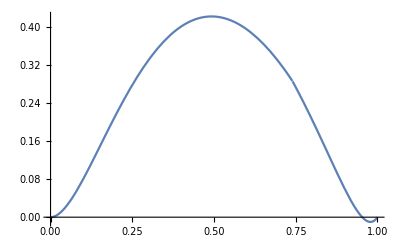

```mathematica
Plot[Piecewise[{{x^3-4 x^2+ b x +ϵ(b(Exp[-x/ϵ]-1)),x<x0},{x^3-4 x^2+ B/2 x +ϵ(B/4(Exp[-2(1-x)/ϵ]-1)),x≥x0}}],{x,0,1}]
```

```mathematica
NDSolve[{(.1)^2 y''''[x]-1/(1-((3x)/4))y''[x]==8,y[0]==0,y'[0]==0,y[1]==0,y'[1]==0},y[x],{x,0,1}]
```

{{y[x]→InterpolatingFunction[{{0., 1.}}, <>][x]}}

```mathematica
%9⟦1,1,2⟧
```

InterpolatingFunction[{{0., 1.}}, <>][x]

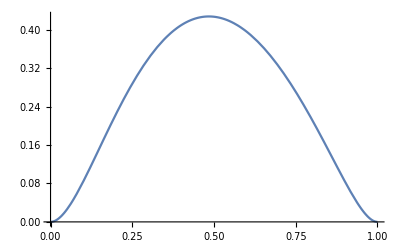

```mathematica
Plot[%,{x,0.,1.}]
```

```mathematica
DSolve[{1/4v''''[x]-v''[x]==2,v[0]==0,v'[0]==0},v[x],{x,0,1}]
```

{{v[x]→1/4 ⅇ^(-2 x) (ⅇ^(4 x) C[1]+C[2]-ⅇ^(2 x) (4 x^2+C[1]+2 x (C[1]-C[2])+C[2]))}}

```mathematica
FullSimplify[%]
```

```mathematica
{{v[x]->ⅇ^-x (-1+ⅇ^x) (ⅇ^x C[1]-C[2])+x (-4x-C[1]+C[2])}}
a:=-1
```

{{v[x]→ⅇ^-x (-1+ⅇ^x) (ⅇ^x C[1]-C[2])+x (-4 x-C[1]+C[2])}}

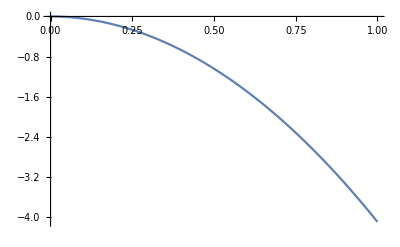

```mathematica
Plot[-4 x^2+a ϵ^2(Exp[-x/ϵ]-1)+a ϵ x,{x,0,1}]
```